```mathematica
Subscript[ρ, pb] = 11.34; (*g/cm^3*)
Subscript[ρ, al] = 2.70; (*g/cm^3*)
i0 = 53963; (* counts*)
LeadThickness = {925.3,1821.3,2648.1,4441.7,7194.1}/(Subscript[ρ, pb]/.001); (*cm*)
LeadPhotoCounts = {28231,25761,23397,20155,12417};
AluminumThickness = {1/2,1,3/2,2}*2.54;(*cm*)
AluminumPhotoCounts = {28540,21082,16263,12113};
```

```mathematica
data=Transpose[{LeadThickness,Log[LeadPhotoCounts/i0]}];
k = Fit[data,{1,x},x];
Show[ListPlot[data,AxesLabel -> {"Thickness","Log Counts"},PlotLabel -> "Lead"],Plot[k,{x,0,6}]]

β = -1/(k[[2]])*x
μ = 1/(β *Subscript[ρ, pb] )
```

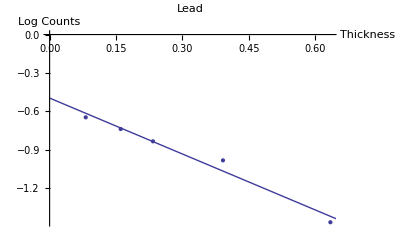
```mathematica
Export["LeadAtenuation.eps",-Graphics-]
```

LeadAtenuation.eps

```mathematica
data=Transpose[{AluminumThickness,Log[AluminumPhotoCounts/i0]}];
k = Fit[data,{1,x},x];
Show[ListPlot[data,AxesLabel -> {"Thickness","Log Counts"},PlotLabel -> "Aluminum"],Plot[k,{x,0,6}]]
β = -1/(k[[2]])*x
μ = 1/(β *Subscript[ρ, al] )
```

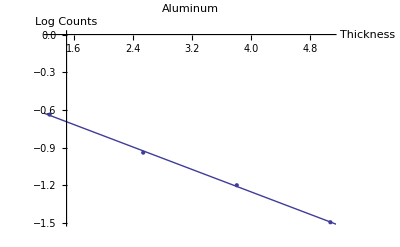
```mathematica
Export["AlAtenuation.eps",-Graphics-]
```

AlAtenuation.eps